# Notebook to solve equation of motion for frictional landslide

## Declare variable values to be used

```mathematica
ClearAll["Global`*"]
tval=1;(*Simulation duration*)
L = 50;(*Discretization of domain - much larger than landslide body*)
Lx = 10;(*Landslide length-scale*)
h0 = 1;(*peak height of the landslide*)
(*frictional parameters*)
Aλ = 0.3;(*This is actually A(1-λ) - accounting for overpressure at the base*)
θ = π/4;(*Average slope of the body*)
```

## Define normalized PDE to be solved, along with BC and IC

Here we assume that the landslide body is a pre-existing mass with some topography distribution h(x,0), and the boundary conditions are h=0 at the edges of the domain.

```mathematica
eqn = D[ h[x,t],t] ==-Exp[(Tan[θ]-h0/Lx*D[h[x,t],x])/Aλ]*(D[h[x,t],x]-h[x,t]/Aλ*h0/Lx*D[h[x,t],x,x])
BC = {h[-L,t]==0,h[L,t]==0};
(*ICfun = 0.5*Erfc[(x+L*2/3)/2];*)
ICfun = Exp[-((x+L/2)/Lx)^4/2]*(1+0.01*Sin[2π x/Lx]);
(*ICfun = Piecewise[{{-h0/L*x,x<0}},0];*)
IC = h[x,0] == ICfun;
sol = NDSolve[{eqn,IC,BC},h,{x,-L,L},{t,0,tval},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100,"MaxPoints"->5000}}];
```

h^(0,1)[x,t]==-ⅇ^(3.33333 (1-1/10 h^(1,0)[x,t])) (h^(1,0)[x,t]-0.333333 h[x,t] h^(2,0)[x,t])

## Plot Initial height and curvature

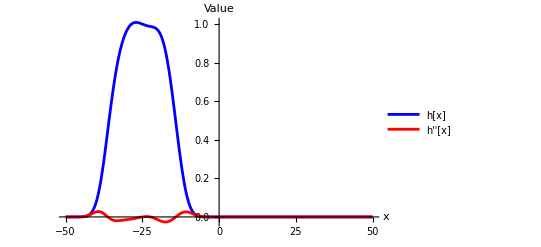

```mathematica
ICgrad = D[ICfun,x,x];
Plot[{ICfun,ICgrad},{x,-L,L},PlotStyle->{Blue,Red},PlotLegends->{"h[x]","h''[x]"},AxesLabel->{"x","Value"},PlotRange->Full]
```

## Plot h[x,t] in linear and log scale

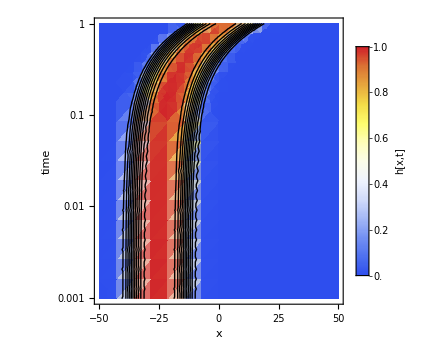
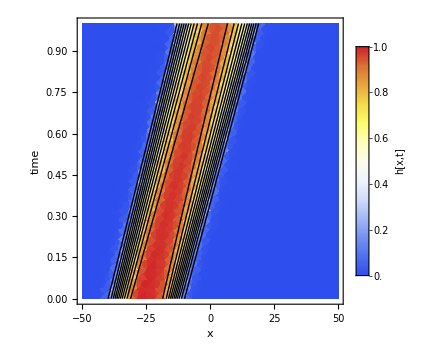

```mathematica
{
{
(*Logarithmic t*)
Show[
DensityPlot[
Evaluate[h[x,t]/. sol],{x,-L,L},{t,0,tval},ColorFunction->"TemperatureMap",PlotLegends->BarLegend[{"TemperatureMap",{0,h0}},LegendLabel->"h[x,t]"], FrameLabel->{"x","time"},
ScalingFunctions->{"Linear","Log"}, ImageSize->Medium,BaseStyle->{FontSize->16},PlotRange->Full
],
ContourPlot[
Evaluate[h[x,t]/. sol],{x,-L,L},{t,0,tval},
Contours->11,(*Number of contour lines*)
ContourStyle->Black,(*Make contours stand out*)
ContourShading->None (*Remove fill to show DensityPlot underneath*),
ScalingFunctions->{"Linear","Log"}, ImageSize->Medium
]
],
(*Linear axes*)
Show[
DensityPlot[
Evaluate[h[x,t]/. sol],{x,-L,L},{t,0,tval},ColorFunction->"TemperatureMap",PlotLegends->BarLegend[{"TemperatureMap",{0,h0}},LegendLabel->"h[x,t]"], FrameLabel->{"x","time"}, ImageSize->Medium,BaseStyle->{FontSize->16},PlotRange->Full
],
ContourPlot[
Evaluate[h[x,t]/. sol],{x,-L,L},{t,0,tval},
Contours->11,(*Number of contour lines*)
ContourStyle->Black,(*Make contours stand out*)
ContourShading->None (*Remove fill to show DensityPlot underneath*),PlotRange->Full, ImageSize->Medium
]
]
}
}
```

### Plot snapshots of h[x,t] at select times

```mathematica
tValues={0,0.01,0.05,0.1,0.2,0.4,0.6,0.8,1.0}*tval; (*Choose different t values*)
Plot[Evaluate@Table[h[x,t]/. sol,{t,tValues}],{x,-L,L},PlotStyle->Table[Directive[Thick,ColorData["WatermelonColors",Rescale[i,{1,Length[tValues]}]]],{i,Length[tValues]}],PlotLegends->Placed[LineLegend[tValues,LabelStyle->{12}],{1.1,0.5}],Frame->True,FrameLabel->{"x","h(x,t)"},LabelStyle->{14,Bold},Axes->False,ImageSize->Large,PlotRange->Full]
```

-Graphics-

### Plot timeseries of h[x,t] at select points in space

```mathematica
xValues={-1,-0.8,-0.6,-0.4,-0.2,0,0.2,0.5}*L; (*Choose different x values*)
Plot[Evaluate@Table[h[x,t]/. sol,{x,xValues}],{t,0,tval},PlotStyle->Table[Directive[Thick,ColorData["Rainbow",Rescale[i,{1,Length[tValues]}]]],{i,Length[xValues]}],PlotLegends->Placed[LineLegend[xValues,LabelStyle->{12}],{1.1,0.5}],Frame->True,FrameLabel->{"t","h(x,t)"},LabelStyle->{14,Bold},Axes->False,ImageSize->Large,PlotRange->Full]
```

-Graphics-